```mathematica
ClearAll["Global`*"]
```

```mathematica
GenDeltaSBot[i_,S_,kin_,Conn_,ProbSnegPrey_]:=kin*2*(S-1)*Conn*Subscript[η, i]*(1-2*ProbSnegPrey);
GenDeltaSTop[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*2*(S-1)*Conn*(1-Subscript[η, i])*(1-2*ProbSnegPred);
GenDeltaSTopPredPlus[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*(1 + (2*(S-1)*Conn*(1-Subscript[η, i]) - 1)*(1-2*ProbSnegPred));
GenDeltaSTopPredMinus[i_,S_,kout_,Conn_,ProbSnegPred_]:=kout*(-1 + (2*(S-1)*Conn*(1-Subscript[η, i]) - 1)*(1-2*ProbSnegPred));
BetaFromMeanVariance[etaMean_,etaVar_]:=Module[{alpha,beta},
alpha=etaMean*((etaMean*(1-etaMean)/etaVar)-1);
beta=(1-etaMean)*((etaMean*(1-etaMean)/etaVar)-1);
BetaDistribution[alpha,beta]];
(*GenDeltaSBot = kin*2*(S-1)*Conn*Subscript[η, i]*(1-2*(ProbSnegPrey));*)
(*GenDeltaSTop =  kout*2*(S-1)*Conn*(1-Subscript[η, i])*(1 - 2*(ProbSnegPred));*)
S=100;
Conn=0.02;
kin=5;
kout=10;
g=10;
maxi = 10;
nicheint = 1/(maxi-1);
(*nichevalues =N[Table[i,{i,1/maxi,(maxi-nicheint)/maxi,nicheint}]]*)
nichevalues =N[Table[i,{i,0,1,nicheint}]]
maxi=Length[nichevalues];
PredEta = Subscript[η, i]+nicheint;
(*EtaDiv = 2;*) (*From earlier Zeno idea*)
(*PredEta = (Subscript[η, i]+1)/EtaDiv; *)
(*PreyEta = EtaDiv*Subscript[η, i] - 1;*)
(*For saving future values*)
ProbSneg =Table[0,{maxi}];
ProbSnegPredPlus=Table[0,{maxi}];
ProbSnegPredMinus=Table[0,{maxi}];
ProbSnegvalues=Table[0,{maxi}];
ProbSnegExpectation=Table[0,{maxi}];
ProbSnegExpectation2 = Table[0,{maxi}];
cascadevalue = Table[0,{maxi}];
ExpectedCascade = Table[0,{maxi}];
```

{0.,0.111111,0.222222,0.333333,0.444444,0.555556,0.666667,0.777778,0.888889,1.}

```mathematica
Table[
If[i==1,
DeltaSBot=g,
(*Put prior ProbSneg functions in terms of Subscript[η, i]*)
ProbSnegPreyList = Table[
x = i-j;
ProbSneg[[j]]/.Subscript[η, j]->(Subscript[η, i]-(i-j)*nicheint),(*Even intervals only*)
(*ProbSneg[[j]]/.{Subscript[η, x]->2^x*Subscript[η, i]-(2^x-1)},*) (*Xeno only*)
{j,1,i-1}];
ProbSnegPrey=(1/(i-1))*Sum[ProbSnegPreyList[[j]],{j,1,i-1}];(*Average all ProbSneg from lower trophic levels*)
DeltaSBot=GenDeltaSBot[i,S,kin,Conn,ProbSnegPrey]
];
(*ProbSnegPred=(1-Subscript[η, i+1]);*)
(*This one ranges from beta to 1-beta*)
(*ProbSnegPred = ( 1-Subscript[η, i+1]+β*(2*Subscript[η, i+1]-1))/.β->0.38;*)
(*ProbSnegPred = 0.1;*)(*(0.4)*(Subscript[η, i+1]) + 0.1;*)
(*ProbSnegPred =0.5+0.1* Log[Subscript[η, i+1]/(1-Subscript[η, i+1])];*)
(*This one ranges from beta to 0.5*)
(*ProbSnegPred =(0.55+(-0.55+β) (1-Subscript[η, i+1]))/.β->0.45;*)
ProbSnegPred = 0.47;
DeltaSTop=GenDeltaSTop[i,S,kout,Conn,ProbSnegPred];
DeltaSTopPredPlus=GenDeltaSTopPredPlus[i,S,kout,Conn,ProbSnegPred];
DeltaSTopPredMinus=GenDeltaSTopPredMinus[i,S,kout,Conn,ProbSnegPred];
(*Distribution across niche axis*)
(*If at top of niche axis, there is no top-down effect*)
If[i==maxi,
ProbSneg[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTop)])/.{Subscript[η, i+1]->1};
ProbSnegPredPlus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredPlus)])/.{Subscript[η, i+1]->1};
ProbSnegPredMinus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredMinus)])/.{Subscript[η, i+1]->1};
,
ProbSneg[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTop)])/.{Subscript[η, i+1]->PredEta};
ProbSnegPredPlus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredPlus)])/.{Subscript[η, i+1]->PredEta};
ProbSnegPredMinus[[i]]= 1 - 1/(1+Exp[-(DeltaSBot- DeltaSTopPredMinus)])/.{Subscript[η, i+1]->PredEta};
];
(*Assume niche value take on exact interval value*)
ProbSnegvalues[[i]] = ProbSneg[[i]]/.Subscript[η, i]->nichevalues[[i]];
(*Assume niche value varies uniformally*)
Quiet[ProbSnegExpectation[[i]]=NIntegrate[ProbSneg[[i]],{Subscript[η, i],0,1}]];
(*Assume niche value varies with Beta Dist*)
If[i==1 ,
meaneta = 0.001,
If[i==maxi,
meaneta=0.999,
meaneta = nichevalues[[i]]]
];
(*Variance: constant? Or near-max?*)
(*vareta = 0.08;*)
vareta = (meaneta*(1-meaneta))*(0.1);(*Variance increases in the middle; declines at ends*)
dist=BetaFromMeanVariance[meaneta,vareta];
Quiet[ProbSnegExpectation2[[i]]=NIntegrate[PDF[dist,Subscript[η, i]]*ProbSneg[[i]],{Subscript[η, i],0,1}]];
(*Calculate Cascades*)
cascadevalue[[i]] = Log[(2 + (1)*(1 -ProbSnegPredPlus[[i]]) + (-1)*ProbSnegPredPlus[[i]])/(2 + (1)*(1 - ProbSnegPredMinus[[i]]) + (-1)*ProbSnegPredMinus[[i]])];
Quiet[ExpectedCascade[[i]]=NIntegrate[PDF[dist,Subscript[η, i]]*cascadevalue[[i]],{Subscript[η, i],0,1}]];
,{i,1,maxi}];
```

```mathematica
GraphicsRow[{
Show[{
ListPlot[Transpose[{nichevalues,ProbSnegvalues}],Joined->True,Frame->True,FrameLabel->{"Niche Value","Prob S-"},PlotRange->{0,All}],
ListPlot[Transpose[{nichevalues,ProbSnegvalues}],Joined->False]}],
If[Conn==0.02,
trophiclevelparams = {A->1.00,B->1.956,alpha->0.74},
If[Conn==0.04,
trophiclevelparams ={A->1, B->2.501,alpha->0.582}(*{A->0.895,B->2.594,alpha->0.540}*),
If[Conn==0.1,
trophiclevelparams = {A->0.76,B->3.921,alpha->0.406}]
]
];
trophiclevels = A+B*nichevalues^alpha/.trophiclevelparams;
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegvalues}],Joined->True,Frame->True,FrameLabel->{"Trophic level","Prob S-"},PlotRange->{0,All}],
ListPlot[Transpose[{trophiclevels,ProbSnegvalues}],Joined->False]}],
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation}],Joined->True,Frame->True,FrameLabel->{"Trophic level","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation}],Joined->False]}],
Show[{
ListPlot[Transpose[{nichevalues,ProbSnegExpectation2}],Joined->True,Frame->True,FrameLabel->{"Niche Value","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{nichevalues,ProbSnegExpectation2}],Joined->False]}],
Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->True,Frame->True,FrameLabel->{"Trophic level","E{Prob S-}"},PlotRange->{-0.01,1}],
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->False]}]
}]
```

-Graphics-

```mathematica
datapropneg = Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/data/n_c_propneg_data_g10_kout10.csv"]];
```

```mathematica
ConnValues = {0.02,0.02};
(*m1values = {0.036,0.14};
m2values = {1.2,0.14};*)
{sampledData,sampledDataSD}=Table[
Cvalue = ConnValues[[i]];
datasubset=Select[datapropneg[[2;;]],#[[2]]==Cvalue&][[All,{6,3}]];
datasubsetSD=Select[datapropneg[[2;;]],#[[2]]==Cvalue&][[All,{6,7}]];
len=Length[datasubset];
sampleCount=50;
(*Generate 100 evenly spaced indices from 1 to len*)
indices=Round[Subdivide[1,len,sampleCount-1]];
(*Get the sampled subset*)
sampledset = datasubset[[indices]];
sampledsetSD = datasubsetSD[[indices]];
(*TL =1 + 11.6*(sampledset[[;;All,1]]*Cvalue)^0.49;*)
(*Transpose[{TL,sampledset[[;;All,2]]}]*)
{Transpose[{sampledset[[;;All,1]],sampledset[[;;All,2]]}],Transpose[{sampledsetSD[[;;All,1]],sampledsetSD[[;;All,2]]}]}
,{i,1,Length[ConnValues]}];
```

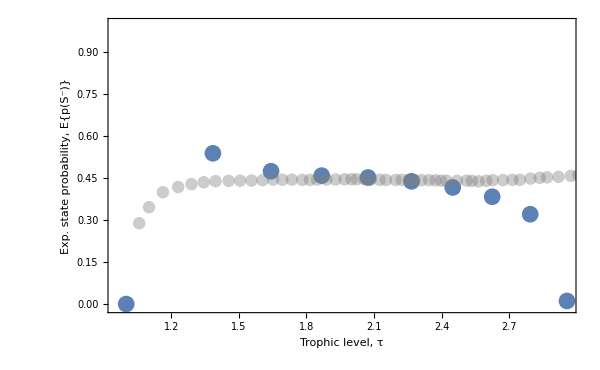

```mathematica
ExpectedProbNegPlot = Show[{
ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],PlotStyle->{ColorData[97,1],PointSize[0.02]},Joined->False,Frame->True,FrameLabel->{Style["Trophic level, τ",FontFamily->"Times New Roman",FontSize->18],Style["Exp. state probability, E{p(S^-)}",FontFamily->"Times New Roman",FontSize->18]},PlotRange->{-0.01,1},LabelStyle->Directive[FontSize->16,Black]],
(*ListPlot[Transpose[{trophiclevels,ProbSnegExpectation2}],Joined->False],*)
ListPlot[sampledData[[1]],PlotStyle->Directive[Opacity[0.4],Gray,PointSize[0.015]],Joined->False,PlotRange->All]
(*,
ListPlot[SDPlus,PlotStyle->{Gray,PointSize[0.02]},Joined->True,PlotRange->All],
ListPlot[SDMinus,PlotStyle->{Gray,PointSize[0.02]},Joined->True,PlotRange->All]*)
},
ImageSize->600]
```

Statistical test of analytical-to-simulation fit

```mathematica
AnalyticalResults = Transpose[{trophiclevels,ProbSnegExpectation2}]
```

{{1.,0.000487427},{1.38479,0.538848},{1.64268,0.474858},{1.86756,0.459193},{2.07338,0.452445},{2.2661,0.438673},{2.44898,0.416732},{2.62406,0.383656},{2.79273,0.321224},{2.956,0.0116666}}

```mathematica
SimulatedResults = sampledData[[1]]
```

{{1.05785,0.289028},{1.10134,0.346296},{1.16309,0.399848},{1.23077,0.418501},{1.28975,0.428795},{1.34435,0.43553},{1.39637,0.439417},{1.45456,0.440294},{1.5054,0.441209},{1.55622,0.441673},{1.60581,0.442825},{1.65177,0.444995},{1.69279,0.444354},{1.73509,0.444869},{1.78163,0.443855},{1.81573,0.444077},{1.84759,0.444992},{1.88893,0.445136},{1.92894,0.445426},{1.96909,0.445992},{2.00005,0.446416},{2.0227,0.446238},{2.05643,0.446483},{2.08493,0.444938},{2.12433,0.444204},{2.15256,0.443768},{2.1952,0.443747},{2.22309,0.44416},{2.25489,0.44372},{2.27877,0.442987},{2.30985,0.44312},{2.34349,0.442801},{2.37249,0.442223},{2.39705,0.441135},{2.42117,0.44055},{2.46793,0.440459},{2.5106,0.4413},{2.53388,0.440157},{2.5636,0.438676},{2.59754,0.440609},{2.62632,0.442794},{2.67166,0.443064},{2.71374,0.444161},{2.74711,0.444199},{2.79402,0.448555},{2.83465,0.451239},{2.86779,0.452905},{2.91812,0.454793},{2.97318,0.458275},{3.00665,0.461015}}

```mathematica
(*analytic points*)
ar=AnalyticalResults;                    (*{{TL,P-}…}*)
(*simulated points;make an interpolation function*)
simF=Interpolation[SimulatedResults,Method->"Spline"];
(*resample simulation at analytic x-values*)
sr=Transpose[{ar[[All,1]],simF/@ar[[All,1]]}];
```

Weighted Root Mean Squared Error

```mathematica
(*Weight included as Gaussian centred on TL≈1.8 with σ=0.5*)
w[x_]:=Exp[-(x-1.8)^2/(2*0.5^2)];
weights=w/@ar[[All,1]];
weights[[1]] = 0; (*the first point should be zero because there is no sim result against which to match*)
errVec=ar[[All,2]]-sr[[All,2]]
wRMSE=Sqrt[Total[(weights*errVec^2)]/Total[weights]]
(*Unweighted RMSE*)
unweights=ConstantArray[1.,Length[ar]];
unweights[[1]] = 0;
RMSE=Sqrt[Total[(unweights*errVec^2)]/Total[unweights]]
```

{-0.196969,0.100014,0.0300613,0.0140193,0.00681262,-0.00465843,-0.0235269,-0.0590212,-0.127208,-0.445334}

0.0707117

0.159761

```mathematica
trophiclevels
```

{1.,1.38479,1.64268,1.86756,2.07338,2.2661,2.44898,2.62406,2.79273,2.956}

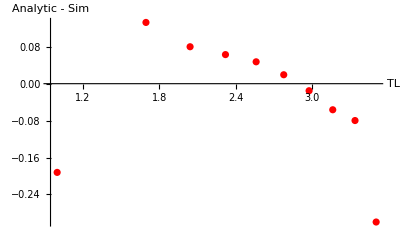

```mathematica
ListPlot[Transpose[{ar[[All,1]],errVec}],AxesLabel->{"TL","Analytic - Sim"},PlotStyle->Red]
```

Except for first point, these provide similar results - if window is chosen such that first point excluded (0.05), the error vec very similar

```mathematica
Δτ=0.05;            (*half-width of the boxcar window;tweak as needed*)
ar=AnalyticalResults; 
simData=SimulatedResults;         (*{{τ,P-} …}*)
movingMean[x_?NumericQ]:=Module[{pts=Select[simData,Abs[#[[1]]-x]<=Δτ&]},If[pts==={},Missing[],Mean[pts[[All,2]]]]];
analyticTL=ar[[All,1]];
maSimValues=movingMean/@analyticTL;
(*keep only rows where we actually have a moving-average value*)
validPos=Position[maSimValues,_Real]//Flatten
arSub=ar[[validPos]];
simSmoothed=maSimValues[[validPos]];
errVec=arSub[[All,2]]-simSmoothed
(*uniform weights except zeros on specific indices,if desired*)
weights=ConstantArray[1.,Length[arSub]]
(*e.g.drop positions 2–4 relative to the*subset*array:*)
(*weights[[{2,3,4}]]=0.;*)
RMSE=Sqrt[Total[weights*errVec^2]/Total[weights]]
```

{2,3,4,5,6,7,8,9,10}

{0.101375,0.030948,0.0141286,0.00673463,-0.00482416,-0.0237724,-0.0584997,-0.126773,-0.444868}

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.159676

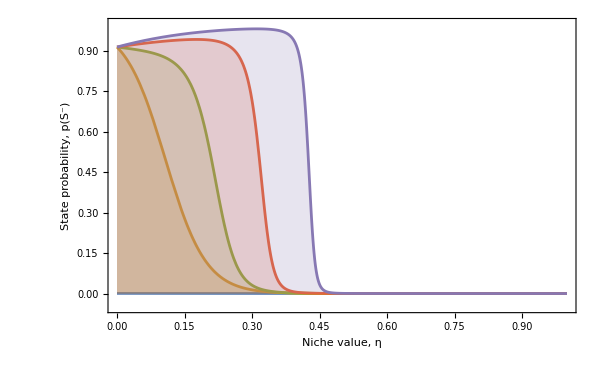

```mathematica
maxdist = 5;
ExpectedProbNegDistPlot=Show[
Table[
Plot[ProbSneg[[k]]/.Table[Subscript[η, j]->Subscript[η, i],{j,1,maxdist}],{Subscript[η, i],0,1},PlotRange->{-0.05,1},Filling->Axis,PlotStyle->ColorData[97,k],Frame->True,FrameLabel->{Style["Niche value, η",FontFamily->"Times New Roman",FontSize->18],Style["State probability, p(S^-)",FontFamily->"Times New Roman",FontSize->18]},LabelStyle->Directive[FontSize->16,Black]],{k,1,maxdist}],ImageSize->600
]
```

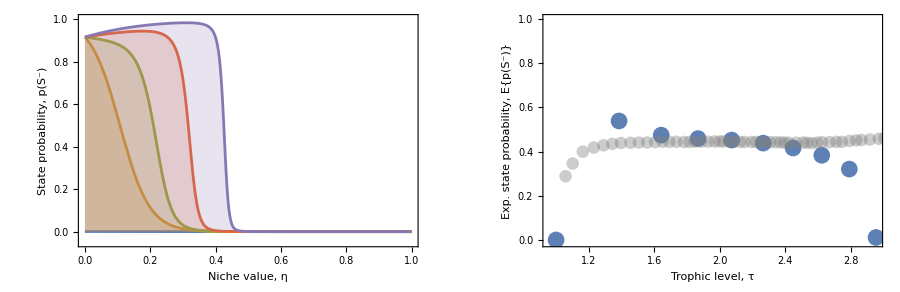

```mathematica
ExpectedProbNeg2PanelPlot = GraphicsRow[{ExpectedProbNegDistPlot,ExpectedProbNegPlot},ImageSize->900]
```

```mathematica
filename = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/figures_prefinal/fig_expectedprobneg_2panel.pdf"}];
Export[filename,ExpectedProbNeg2PanelPlot];
```

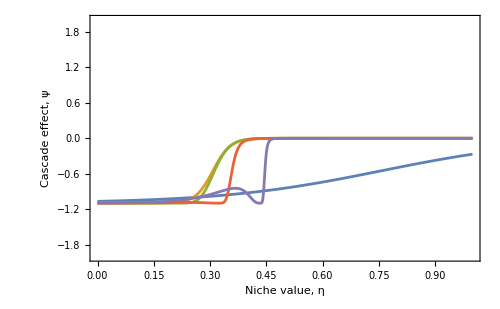

```mathematica
maxdist = 5;
ExpectedCascadeDistPlot=Show[
Table[
Plot[cascadevalue[[k]]/.Table[Subscript[η, j]->Subscript[η, i],{j,1, maxdist}],{Subscript[η, i],0,1},PlotRange->{-2,2},Filling->None,PlotStyle->ColorData[97,k],Frame->True,FrameLabel->{Style["Niche value, η",FontFamily->"Times New Roman",FontSize->18],Style["Cascade effect, ψ",FontFamily->"Times New Roman",FontSize->18]},LabelStyle->Directive[FontSize->16,Black]],{k,1,maxdist}],ImageSize->500
]
```

```mathematica
tlcascadesim = Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/data/tlcascadeC04.csv"]];
tlcascadesimdata =tlcascadesim [[2;;,All]];
```

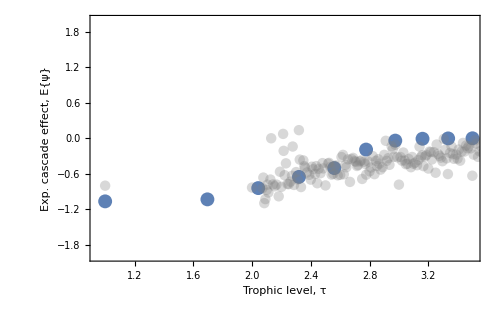

```mathematica
ExpectedCascadePlot=
Show[{
ListPlot[Transpose[{trophiclevels,ExpectedCascade}],PlotStyle->{ColorData[97,1],PointSize[0.02]},Joined->False,Frame->True,FrameLabel->{Style["Trophic level, τ",FontFamily->"Times New Roman",FontSize->18],Style["Exp. cascade effect, E{ψ}",FontFamily->"Times New Roman",FontSize->18]},PlotRange->{-2,2},LabelStyle->Directive[FontSize->16,Black],ImageSize->500],
ListPlot[tlcascadesimdata,PlotStyle->Directive[Opacity[0.3],Gray,PointSize[0.015]]]
}]
```

```mathematica
Δτ=0.15;            (*half-width of the boxcar window;tweak as needed*)
ar=Transpose[{trophiclevels,ExpectedCascade}];  
simData=tlcascadesimdata;          (*{{τ,P-} …}*)
movingMean[x_?NumericQ]:=Module[{pts=Select[simData,Abs[#[[1]]-x]<=Δτ&]},If[pts==={},Missing[],Mean[pts[[All,2]]]]];
analyticTL=ar[[All,1]];
maSimValues=movingMean/@analyticTL;
(*keep only rows where we actually have a moving-average value*)
validPos=Position[maSimValues,_Real]//Flatten;
arSub=ar[[validPos]];
simSmoothed=maSimValues[[validPos]];
errVec=arSub[[All,2]]-simSmoothed
(*uniform weights except zeros on specific indices,if desired*)
weights=ConstantArray[1.,Length[arSub]]
(*e.g.drop positions 2–4 relative to the*subset*array:*)
(*weights[[{2,3,4}]]=0.;*)
RMSE=Sqrt[Total[weights*errVec^2]/Total[weights]]
```

{-0.26562,-0.0649751,-0.108042,-0.000390842,0.243869,0.335459,0.326222,0.268289,0.217535}

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.231942

```mathematica
(*---parameters---------------------------------------------------*)Δτ=0.10;          (*half-width of the window*)
q=0.2;          (*lower-tail probability:0.05=5 % quantile*)
(*---moving lower-quantile over simulation points-----------------*)
movingLower[x_?NumericQ]:=Module[{pts=Select[simData,Abs[#[[1]]-x]<=Δτ&]},If[pts==={},Missing[],Quantile[pts[[All,2]],q]]];
analyticTL=ar[[All,1]];
lbSimValuesRaw=movingLower/@analyticTL;

validPos=Position[lbSimValuesRaw,_Real]//Flatten;
arSub=ar[[validPos]];
lbSimValues=lbSimValuesRaw[[validPos]];

(*signed “edge error”:analytic–lower-bound*)
errVecLB=arSub[[All,2]]-lbSimValues;
weights=ConstantArray[1.,Length[arSub]]
(*e.g.drop positions 2–4 relative to the*subset*array:*)
(*weights[[{2,3,4}]]=0.;*)
RMSELB=Sqrt[Total[weights*errVecLB^2]/Total[weights]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.309614

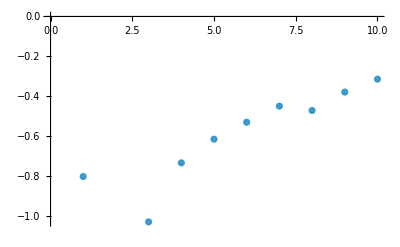

```mathematica
ListPlot[lbSimValuesRaw]
```

```mathematica
(*analytic points*)
ar=Transpose[{trophiclevels,ExpectedCascade}];                    (*{{TL,P-}…}*)
(*simulated points;make an interpolation function*)
simF=Interpolation[tlcascadesimdata,Method->"Spline"];
(*resample simulation at analytic x-values*)
sr=Transpose[{ar[[All,1]],simF/@ar[[All,1]]}];
```

Weighted Root Mean Squared Error

```mathematica
(*indices of analytic points to ignore*)
drop={2,3,4};                       (*1-based*)
(*uniform weights everywhere …*)
weights=ConstantArray[1.,Length[ar]];
(*… except for the rows we want to exclude*)
weights[[drop]]=0.;
errVec=ar[[All,2]]-sr[[All,2]]

wRMSE=Sqrt[Total[weights*errVec^2]/Total[weights]]
```

{-0.062903,238.939,142.615,32.4416,0.212341,-0.706323,-0.0388134,-0.109358,-0.594535,0.0108838}

0.361543

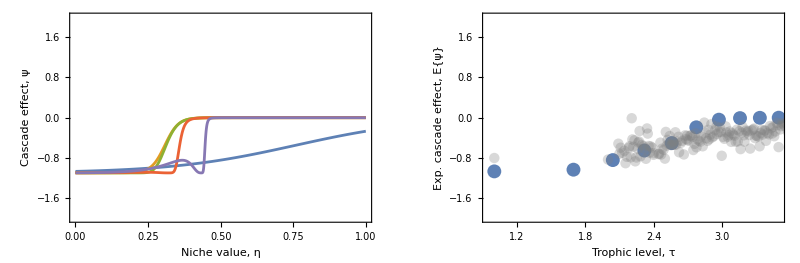

```mathematica
CascadePlot = GraphicsRow[{
ExpectedCascadeDistPlot,
ExpectedCascadePlot
},ImageSize->800]
```

```mathematica
filename = StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_trophicspinglass/trophicspinglass/figures_prefinal/fig_expectedcascade_C04.pdf"}];
Export[filename,CascadePlot];
```